{-1.77,-0.95,0.,3.04,5.06,5.88}

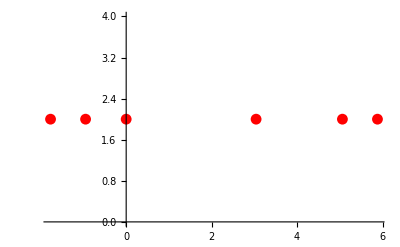

```mathematica
spectrum = {-3.07, -2.25, Mean[{-1.48, -1.12}], Mean[{1.56, 1.92}], 3.76, 4.58};
spectrum = spectrum - spectrum[[3]]
theo = ListPlot[Transpose[{spectrum, Table[2, {i, 1, Length[spectrum]}]}], PlotRange->All, PlotStyle-> {Red}]
```

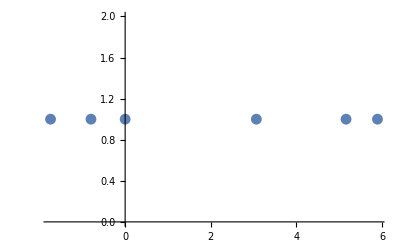

-Graphics-

```mathematica
expdata = {5.892531343806609,5.159004812722334,3.0640494581957114,0.0,-0.7978716587721006,-1.7422686420530307};
exp = ListPlot[Transpose[{expdata, Table[1, {i, 1, Length[expdata]}]}], PlotRange->All]
expdata2 = {-1.7422686420530307,-0.7978716587721006,0.0,3.0640494581957114,5.159004812722334,5.892531343806609};
exp2 = ListPlot[Transpose[{expdata2, Table[1, {i, 0.75, Length[expdata]}]}], PlotRange->All]
```

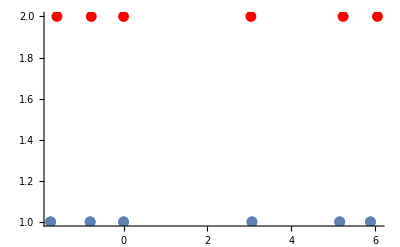

```mathematica
Show[theo, exp, exp2, PlotRange-> All]
```

{{-1.59,5.89253},{-0.77,5.159},{0.,3.06405},{3.04,0.},{5.24,-0.797872},{6.06,-1.74227}}

FittedModel[3.87162-0.972809 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 3.87162 | 0.370507 | 10.4495 | 0.000473922
b | -0.972809 | 0.103733 | -9.37801 | 0.000720252

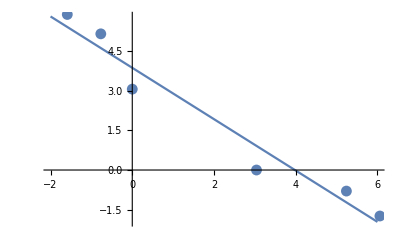

```mathematica
data = Transpose[{spectrum, expdata}]
nlm = NonlinearModelFit[data, a + b x, {a, b}, x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm], {x, -2, 6}],ListPlot[data]]
```

{{-1.77,-1.74227},{-0.95,-0.797872},{0.,0.},{3.04,3.06405},{5.06,5.159},{5.88,5.89253}}

FittedModel[0.0575178+0.997366 x]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0575178 | 0.0319963 | 1.79764 | 0.146641
b | 0.997366 | 0.00914461 | 109.066 | 4.2379×10^-8

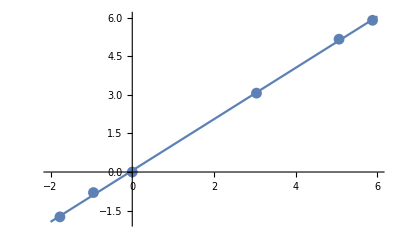

```mathematica
data2 = Transpose[{spectrum, expdata2}]
nlm2 = NonlinearModelFit[data2, a + b x, {a, b}, x]
nlm2["ParameterTable"]
Show[Plot[Normal[nlm2], {x, -2, 6}],ListPlot[data2]]
```